# ICULinkDemo

## “ICULink” Paclet

```mathematica
PacletDirectoryUnload["~/wr/stash/com/ICULink"];
PacletDirectoryLoad["~/wr/stash/com/ICULink"];
```

```mathematica
PacletObject["ICULink"]
```

PacletObject[…]

```mathematica
Needs["ICULink`"]
```

## CompiledComponent

### CompiledComponent[“ICULink”]

```mathematica
cc=CompiledComponent["ICULink"]
```

CompiledComponent[…]

```mathematica
cc["ExternalLibraries"]
```

{libicudata,libicuuc,libicui18n,libicuio,libicutu}

```mathematica
cc["Declarations"]//Shallow
```

{TypeDeclaration[Macro,UChar,UnsignedInteger16],TypeDeclaration[Macro,UChar32,Integer32],TypeDeclaration[Macro,UCharNameChoice,CInt],TypeDeclaration[Macro,UErrorCode,CInt],TypeDeclaration[Macro,UProperty,CInt],TypeDeclaration[Macro,UPropertyNameChoice,CInt],LibraryFunctionDeclaration[u_charName_62,ICULink`CC`Character`Private`$ICULibraryPaths,Rule[«2»],Rule[«2»],Rule[«2»]],LibraryFunctionDeclaration[u_charAge_62,ICULink`CC`Character`Private`$ICULibraryPaths,Rule[«2»],Rule[«2»],Rule[«2»]],LibraryFunctionDeclaration[u_getIntPropertyValue_62,ICULink`CC`Character`Private`$ICULibraryPaths,Rule[«2»],Rule[«2»],Rule[«2»]],LibraryFunctionDeclaration[u_getPropertyValueName_62,ICULink`CC`Character`Private`$ICULibraryPaths,Rule[«2»],Rule[«2»],Rule[«2»]],«8»}

```mathematica
cc["InstalledFunctions"]//List@@@Normal@#&//TableForm
```

ICULink`CC`ICUCharacterName | ICULink`CC`ICUCharacterName
ICULink`CC`ICUCharacterNameAlias | ICULink`CC`ICUCharacterNameAlias
ICULink`CC`ICUCharacterAge | ICULink`CC`ICUCharacterAge
ICULink`CC`ICUCharacterPropertyValueName | ICULink`CC`ICUCharacterPropertyValueName
ICULink`CC`UnicodeVersion | ICULink`CC`UnicodeVersion

### Build Component

```mathematica
BuildCompiledComponent["ICULink",PacletObject["ICULink"],]
```

/usr/bin/clang -dynamiclib -o "/Users/daniels/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-ARM64/Working-m6502-50198-4202438144-1/ICULink-1b16c2fd-9586-4946-883d-bd00511479bf.dylib" -arch arm64 -mmacosx-version-min=11.0 -install_name @rpath/ICULink-1b16c2fd-9586-4946-883d-bd00511479bf.dylib -fPIC -O2  -I"/Applications/M14.0.0.app/Contents/SystemFiles/IncludeFiles/C" -I"/Applications/M14.0.0.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-ARM64/CompilerAdditions" "/Users/daniels/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-ARM64/Working-m6502-50198-4202438144-1/ICULink-1b16c2fd-9586-4946-883d-bd00511479bf.c" "/private/var/folders/00/636pzksx2872qfsw8wzbb4cr0000gn/T/m000003501981.obj" -F"/Applications/M14.0.0.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-ARM64/CompilerAdditions" -L"/Applications/M14.0.0.app/Contents/SystemFiles/Libraries/MacOSX-ARM64"  -framework "mathlink" "/Applications/M14.0.0.app/Contents/SystemFiles/Links/DICOMTools/LibraryResources/MacOSX-ARM64/libicudata.dylib" "/Applications/M14.0.0.app/Contents/SystemFiles/Links/DICOMTools/LibraryResources/MacOSX-ARM64/libicuuc.dylib" "/Applications/M14.0.0.app/Contents/SystemFiles/Links/CalendarTools/LibraryResources/MacOSX-ARM64/libicui18n.dylib" "/Applications/M14.0.0.app/Contents/SystemFiles/Links/CalendarTools/LibraryResources/MacOSX-ARM64/libicuio.dylib" "/Applications/M14.0.0.app/Contents/SystemFiles/Links/CalendarTools/LibraryResources/MacOSX-ARM64/libicutu.dylib" "/Users/daniels/wr/stash/com/Compile/CompiledLibrary/LibraryResources/MacOSX-ARM64/WolframCompilerStrings.dylib" "/Users/daniels/wr/stash/com/Compile/CompiledCompiler/LibraryResources/MacOSX-ARM64/CompilerCoreRuntime.dylib" "/Applications/M14.0.0.app/Contents/SystemFiles/Libraries/MacOSX-ARM64/libWolframRTL_Kernel.dylib" "/Applications/M14.0.0.app/Contents/SystemFiles/Libraries/MacOSX-ARM64/libWolframEngine.dylib" "/Applications/M14.0.0.app/Contents/SystemFiles/Components/LLVMLink/LLVMResources/MacOSX-ARM64/lib/libclang_rt.osx.a" "/Applications/M14.0.0.app/Contents/SystemFiles/Libraries/MacOSX-ARM64/libomp.dylib" -lc++ -framework Foundation 2>&1

Success[…]

### Load Component

#### UnicodeVersion

```mathematica
AbsoluteTiming[ICULink`CC`UnicodeVersion[]]
```

{0.664525,{11,0,0,0}}

```mathematica
RepeatedTiming[ICULink`CC`UnicodeVersion[]]
```

{7.69326×10^-7,{11,0,0,0}}

#### CharacterName

```mathematica
ICULink`CC`CharacterName[32]//RepeatedTiming
```

{1.58629×10^-6,SPACE}

```mathematica
Dataset[Table[<|"Code"->i,"Name"->ICULink`CC`CharacterName[i]|>,{i,32,255}]]
```

#### CharacterAge

```mathematica
ICULink`CC`CharacterAge[32]//RepeatedTiming
```

{7.75857×10^-7,{1,1,0,0}}

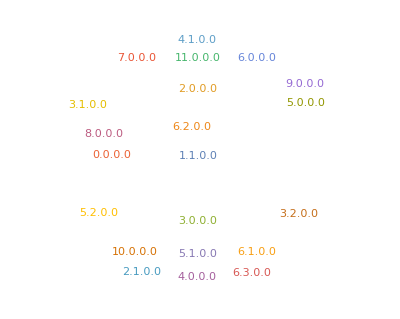

```mathematica
WordCloud[Table[StringRiffle[ICULink`CC`CharacterAge[i],"."],{i,0,65535}]]
```

## ForeignFunctionInterface

#### UnicodeVersion

```mathematica
AbsoluteTiming[ICULink`FFI`UnicodeVersion[]]
```

{0.005305,{11,0,0,0}}

```mathematica
RepeatedTiming[ICULink`FFI`UnicodeVersion[]]
```

{0.0000351073,{11,0,0,0}}

#### CharacterName

```mathematica
ICULink`FFI`CharacterName[32]//RepeatedTiming
```

{0.0000448818,SPACE}

```mathematica
Dataset[Table[<|"Code"->i,"Name"->ICULink`FFI`CharacterName[i]|>,{i,32,255}]]
```

#### CharacterAge

```mathematica
ICULink`FFI`CharacterAge[32]//RepeatedTiming
```

{0.0000383048,{1,1,0,0}}

```mathematica
WordCloud[Table[StringRiffle[ICULink`FFI`CharacterAge[i],"."],{i,0,65535}]]
```

-Graphics-